```mathematica
BordersUnsorted[f_]:=Module[{edgs},
  edgs=Flatten[Map[{
   {Part[#,1],Part[#,2]},
   {Part[#,2],Part[#,3]},
   {Part[#,3],Part[#,1]},
   {Part[#,2],Part[#,1]},
   {Part[#,3],Part[#,2]},
  {Part[#,1],Part[#,3]}
  }&,f],1];
DeleteDuplicates[Flatten[Part[Select[Tally[edgs],Last[#]==1&],;;,1]]]
];

TriangleArea[tri_]:=0.5Norm[Cross[Part[tri,2]-Part[tri,1],Part[tri,3]-Part[tri,1] ]];

InverseMassMatrix[v_,f_]:=Module[{ar},
ar=ConstantArray[.0,Length[v]];
Scan[Part[ar,#]+=TriangleArea[Part[v,#]]/3&,f];
SparseArray[MapIndexed[{First[#2],First[#2]}->#1&,1./ar]]
];
```

```mathematica
AngleDefect[objfile_,returnOnlyInner_:True,normalize_:False]:=Module[{brd,inner,angleDefect,input,v,f},
input=Import[objfile,"GraphicsComplex"];
v=Part[input,1];
Clear[x];
f=Flatten[Cases[input,Triangle[x_]->x,Infinity],1];
brd=BordersUnsorted[f];
inner=Complement[Range[Length[v]],brd];
angleDefect=ConstantArray[-2π,Length[v]];

Map[Function[fi,
Table[
Module[{a,k1,k2,e1,e2},
k1=Mod[k,3]+1;
k2=Mod[k+1,3]+1;
e1=Part[v,Part[fi,k1]]-Part[v,Part[fi,k]];
e2=Part[v,Part[fi,k2]]-Part[v,Part[fi,k]];
a=ArcCos[e1.e2/ (Norm[e1] *Norm[e2])];
Part[angleDefect,Part[fi,k]] +=a;
],{k,3}]
],f];

If[normalize,angleDefect=InverseMassMatrix[v,f].angleDefect]; 

Part[angleDefect,brd]=.0;
If[returnOnlyInner,Part[angleDefect,inner],angleDefect]
];
```

```mathematica
(*file="D:\\Dropbox\\ETH\\2019-SIGGRAPH-Developable surfaces (Olga, alex)\\Results\\results for paper\\_all paper results for K evaluation\\2.1 bumpy side 5p.obj";*)
(*file="D:\\Dropbox\\ETH\\2019-SIGGRAPH-Developable surfaces (Olga, alex)\\Results\\results for paper\\_all paper results for K evaluation\\2.2 bumpy side 11p.obj";*)
(*file="D:\\Dropbox\\ETH\\2019-SIGGRAPH-Developable surfaces (Olga, alex)\\Results\\results for paper\\_all paper results for K evaluation\\12.1 bumpy cube.obj";*)
file="D:\\Dropbox\\ETH\\2019-SIGGRAPH-Developable surfaces (Olga, alex)\\Results\\results for paper\\_all paper results for K evaluation\\12.2 dog.obj";
(*file="D:\\Dropbox\\ETH\\2019-SIGGRAPH-Developable surfaces (Olga, alex)\\Results\\results for paper\\_all paper results for K evaluation\\";
file="D:\\Dropbox\\ETH\\2019-SIGGRAPH-Developable surfaces (Olga, alex)\\Results\\results for paper\\_all paper results for K evaluation\\";file="D:\\Dropbox\\ETH\\2019-SIGGRAPH-Developable surfaces (Olga, alex)\\Results\\results for paper\\_all paper results for K evaluation\\";file="D:\\Dropbox\\ETH\\2019-SIGGRAPH-Developable surfaces (Olga, alex)\\Results\\results for paper\\_all paper results for K evaluation\\";file="D:\\Dropbox\\ETH\\2019-SIGGRAPH-Developable surfaces (Olga, alex)\\Results\\results for paper\\_all paper results for K evaluation\\";file="D:\\Dropbox\\ETH\\2019-SIGGRAPH-Developable surfaces (Olga, alex)\\Results\\results for paper\\_all paper results for K evaluation\\";
*)
```

0.00468863

0.000697262

4.56079×10^-7

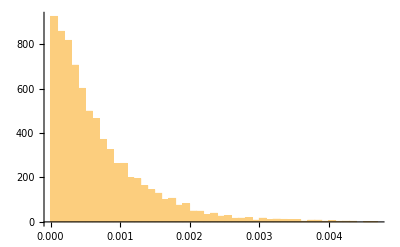

```mathematica
ad=Abs[AngleDefect[file]];
Max[ad]
Mean[ad]
Variance[ad]
Histogram[ad,PlotRange->All]
```

0.410709

0.00354221

0.000117434

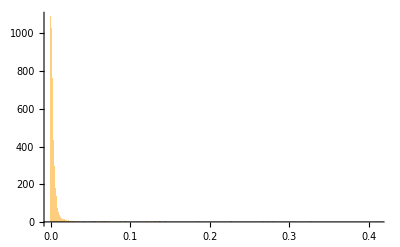

```mathematica
adNorm=Abs[AngleDefect[file, True, True]];
Max[adNorm]
Mean[adNorm]
Variance[adNorm]
Histogram[adNorm,PlotRange->All]
```

```mathematica
ad2=Abs[AngleDefect[file,False]];
```

```mathematica
input=Import[file,"GraphicsComplex"];
v=Part[input,1];
f=Flatten[Cases[input,Triangle[x_]->x,Infinity],1];
cl=ColorData["CherryTones"]/@(0.1+0.9Rescale[ad2]);
```

```mathematica
Graphics3D[
{
EdgeForm[],
GraphicsComplex[v,Polygon[f],VertexColors->cl]
},Boxed->False
]
```

-Graphics3D-